# H2 VQE on Superconducting Qubits

Set environment, such as threads, gpu, etc.

```mathematica
(*SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];*)
```

Load the QuESTLink

```mathematica
(*Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];*)
```

Virtual quantum devices, loaded after questlink

frequency unit: MHz
time unit: μs

```mathematica
Options[SuperconductingHub]={
(* The number of qubits should match all assignments. Qubits are numbered from 0 to N-1 *)
qubitsNum->6,
(* The T1 time *)
T1-><|0->63,1->93,2->109,3->115,4->68,5->125|>,
(* The T2 time with Hahn echo applied *)
T2-><|0->113,1->149,2->185,3->161,4->122,5->200|>,
(* Excited population probability in the initialisation, also the thermal state *)
ExcitedInit-><|0->0.032,1->0.021,2->0.008,3->0.009,4->0.025,5->0.007|>,
(* Each qubit frequency in MHz   *)
QubitFreq-><|0->4500,1->4900,2->4700,3->5100,4->4900,5->5300|>,
(* Exchange coupling strength of the resonators. Use [Esc]o-o[Esc] for notation *)
ExchangeCoupling-><|0<->1->4,0<->2->1.5,1<->3->1.5,2<->3->4,2<->4->1.5,3<->5->1.5,4<->5->4|>,
(* Transmon Anharmonicity in MHz *)
Anharmonicity-><|0->296.7,1->298.6,2->297.4,3->298.3,4->297.2,5->299.1|>,
(* Fidelity of qubit readout *)
FidRead-><|0->0.9,1->0.92,2->0.96,3->0.97,4->0.93,5->0.97|>,
(* Measurement duration in μs. It is done without quantum amplifiers *)
DurMeas->5,
(* Duration of the Rx and Ry gates are the same regardless the angle. Rz is virtual and perfect. *)
DurRxRy->0.05,
(* Duration of the cross resonance ZX gate that is fixed regardless the angle. The error is sourced from the passive noise only. *)
DurZX->0.5,
(* Duration of the sizzle gate is fixed regardless the angle that is fixed regardless the angle. The error is sourced from the passive noise only. *)
DurZZ->0.5,
(* switches to turn/off some noise*)
StdPassiveNoise->True,
ZZPassiveNoise->True
};
```

## The exact solution

```mathematica
(* molecule distances *)
moldists=DeleteDuplicates@Flatten@{Range[0.35,1.,0.04],Range[1.,2.5,0.1],Range[2.5,5,0.25]}
```

{0.35,0.39,0.43,0.47,0.51,0.55,0.59,0.63,0.67,0.71,0.75,0.79,0.83,0.87,0.91,0.95,0.99,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.75,3.,3.25,3.5,3.75,4.,4.25,4.5,4.75,5.}

```mathematica
(* ground states of H2 *)
gsH2=Table[
	fname=ToString@StringForm["H2_hamiltonians/H2_``.txt", NumberForm[dist, {4, 2}]];
       {ham, nterms, nq} = FormatHamiltonian[fname];
 <|
"distance"->dist,
"hamfile"->fname,
"hamiltonian"->ham,
"groundstate"->Min@Eigenvalues@CalcPauliStringMatrix@ham
|>
,{dist,moldists}];
```

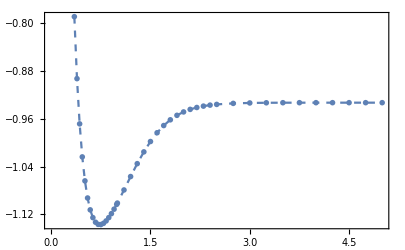

```mathematica
ListPlot[gsH2[[All,{"distance","groundstate"}]],PlotMarkers->{"OpenMarkers",6},PlotStyle->Dashed,Joined->True,Frame->True]
```

## VQE on the virtual device using random ansatz methode

All measurements are perfect here.

### (1) Original noisy setting: H2onSQC0.mx

```mathematica
H2onSQC0={};
```

```mathematica
Table[
{distance,hamfile,hamiltonian,groundstate}=Values@data;
dev=SuperconductingHub[];
conf=DefaultConfig[dev,hamiltonian];
conf["groundstate"]=groundstate;
   res=VQEonVQD[conf];
{runtime,cost,Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,elimmerge,elimbfsmall,elimmetov,elimbf}=res;
AppendTo[H2onSQC0,<|"runtime"->runtime,"ansatz"->ansatz,"θvars"->θvars,"groundstate"->groundstate,"cost"->cost,"fev"->fev|>];
DumpSave["H2onSQC0.mx",H2onSQC0];
Print["dist ",distance," ; runtime ",runtime," ; ϵ=",Last@Elist-conf["groundstate"]];
Print[ListPlot[Elist,ImageSize->300]];
Print[DrawCircuit[ansatz,6]];
,{data,gsH2}]
```

Compilation with automatically generated ansatz at Mon 20 Feb 2023 16:09:35 with grad NGAN

$Aborted